```mathematica
accumsnowlist = {0,28.75269,81.69826};
(*DateandTime = Table[DateObject[{2019,1,20,i}],{i,00,48,03}]*)
DateandTime = Table[DateObject[{2019,1,20,i}],{i,12,18,03}]
accumsnowdata=Transpose[{DateandTime,accumsnowlist}]
```

{Hour: Sun 20 Jan 2019 12 pmGMT-4.,Hour: Sun 20 Jan 2019 03 pmGMT-4.,Hour: Sun 20 Jan 2019 06 pmGMT-4.}

{{Hour: Sun 20 Jan 2019 12 pmGMT-4.,0},{Hour: Sun 20 Jan 2019 03 pmGMT-4.,28.7527},{Hour: Sun 20 Jan 2019 06 pmGMT-4.,81.6983}}

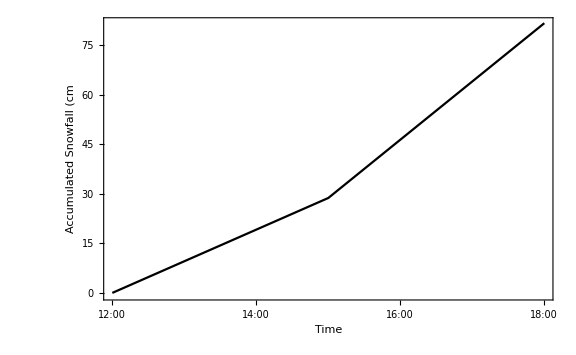

```mathematica
DateListPlot[accumsnowdata,Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm"},PlotStyle->{PointSize[0.01],Darker[Black]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{-.5,Automatic}},ImageSize->Large]
```